```mathematica
Quit[]
```

```mathematica
myData = importDataFrom["OD600.txt"];
timeOd600 = getTimeArray[myData];
```

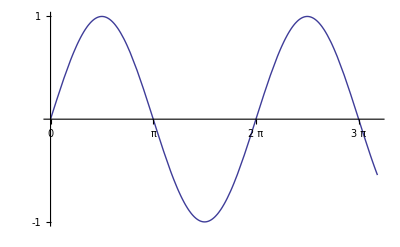

```mathematica
Plot[Sin[x],{x,0,10},Ticks->{{0,Pi,2 Pi,3 Pi},{-1,1}}]
```

```mathematica
Export["graphArray.pdf",
GraphicsGrid[
{
{
generatePlotOfColumn[myData,4],
generatePlotOfColumn[myData,5],
generatePlotOfColumn[myData,6],
generatePlotOfColumn[myData,7],
generatePlotOfColumn[myData,8]
},
{
generatePlotOfColumn[myData,4],
generatePlotOfColumn[myData,5],
generatePlotOfColumn[myData,6],
generatePlotOfColumn[myData,7],
generatePlotOfColumn[myData,8]
}
}
]
]
```

graphArray.pdf

```mathematica
graphHolder = IdentityMatrix[8];
counter = 4;
For[i=1,i<3+1,i++,
For[j=1,j<3+1,j++,
Print[counter, " i=", i, ", j=",j];
Print[graphHolder[[i,j]]];
graphHolder[[i,j]] = generatePlotOfColumn[myData,5];
counter+=1;
]
Print["\n"];
]
```

4 i=1, j=1

1

```mathematica
counter
```

5

```mathematica
graphHolder//MatrixForm
```

```mathematica
graphHolder[[1,2]] = generatePlotOfColumn[myData,5];
```

```mathematica
k=4;
```

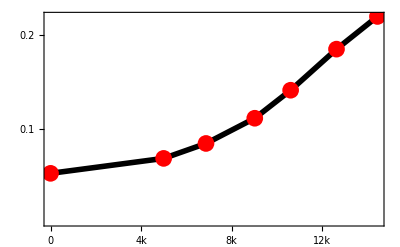
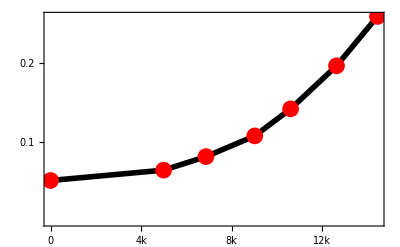
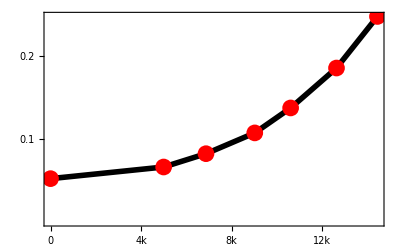
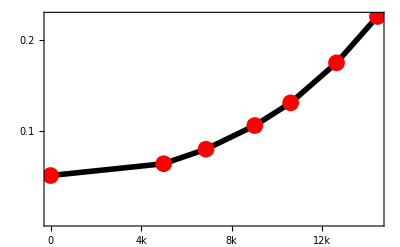
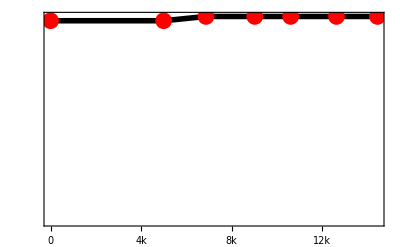
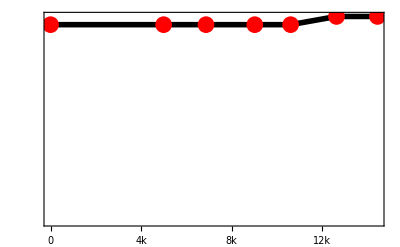
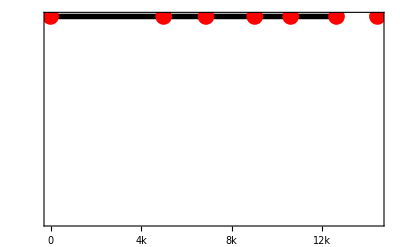
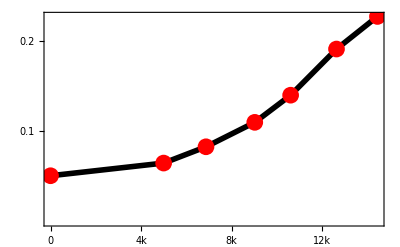
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[k++;generatePlotOfColumn[myData,k], 
{i,1,5},
{j,1,5}
]
```